# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Desktop\\QMB.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# <r>

```mathematica
L=8;
```

```mathematica
J=1;
glist=Table[10^i,{i,-5,1.3,0.1}];
newglist=Partition[glist,4];
h=1;
```

```mathematica
DistributeDefinitions[IsingHamiltonian,BlockDiagonalize];
data1={};
SetSharedVariable[data1];
Do[
ParallelDo[
	Module[{Ha, system,eveneigenval,oddeigenval},

Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
eveneigenval=Quiet[Eigenvalues[system[[1]]]];
oddeigenval=Quiet[Eigenvalues[system[[2]]]];

AppendTo[data1,{{g,Quiet[MeanLevelSpacingRatio[eveneigenval]]},{g,Quiet[MeanLevelSpacingRatio[oddeigenval]]}}];
	]
, {g,k},Method->"CoarsestGrained"];
,{k,newglist}];
Export["r_L_"<>ToString[L]<>"_h_1_LRN.m",Quiet[Sort[data1]]];
```

```mathematica
g=1;
hlist=Table[10^i,{i,-4,1.1,0.1}];
newhlist=Partition[hlist,4];
```

```mathematica
DistributeDefinitions[IsingHamiltonian,BlockDiagonalize];
data1={};
SetSharedVariable[data1];
Do[
ParallelDo[
	Module[{Ha, system,eveneigenval,oddeigenval},

Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
eveneigenval=Quiet[Eigenvalues[system[[1]]]];
oddeigenval=Quiet[Eigenvalues[system[[2]]]];

AppendTo[data1,{{h,Quiet[MeanLevelSpacingRatio[eveneigenval]]},{h,Quiet[MeanLevelSpacingRatio[oddeigenval]]}}];
	]
, {h,k},Method->"CoarsestGrained"];
,{k,newglist}];
Export["r_L_"<>ToString[L]<>"_g_1_SRN.m",Quiet[Sort[data1]]];
```

Divide::infy: Infinite expression (6.63452×10^-11)/0. encountered.

Power::infy: Infinite expression 1/0. encountered.

Min::nord: Invalid comparison with ComplexInfinity attempted.

Divide::infy: Infinite expression (4.44089×10^-16)/0. encountered.

Power::infy: Infinite expression 1/0. encountered.

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

```mathematica
DistributeDefinitions[IsingHamiltonian,BlockDiagonalize];
data1={};
SetSharedVariable[data1];
Do[
ParallelDo[
	Module[{Ha, system,eveneigenval,oddeigenval},

Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
eveneigenval=Quiet[Eigenvalues[system[[1]]]];
oddeigenval=Quiet[Eigenvalues[system[[2]]]];

AppendTo[data1,{{g,Quiet[MeanLevelSpacingRatio[eveneigenval]]},{g,Quiet[MeanLevelSpacingRatio[oddeigenval]]}}];
	]
, {g,k},Method->"CoarsestGrained"];
,{k,newglist}];
Export["r_L_"<>ToString[L]<>"_h_1_LRN.m",Quiet[Sort[data1]]];
```

```mathematica
L=8;
```

```mathematica
Ha=IsingHamiltonian[1,0.5,1,L,BoundaryConditions->"Periodic"];
```

```mathematica
system=BlockDiagonalize[Ha,Symmetry->"Translation"];
```

```mathematica
system
```

BlockDiagonalMatrix[…]

# Results

```mathematica
J=1;
glist=Table[10^i,{i,-5,1.3,0.1}];
newglist=Partition[glist,4];
hlist=Table[10^i,{i,-4,1.1,0.1}];
newhlist=Partition[hlist,4];
```

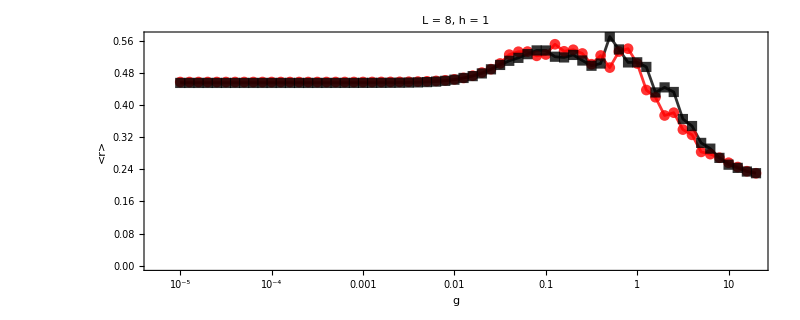

```mathematica
plot=ListLogLinearPlot[{Transpose[{glist,data1[[All,1]][[All,2]]}],Transpose[{glist,data1[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Directive[Red,Opacity[0.8]],Directive[Black,Opacity[0.8]]},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

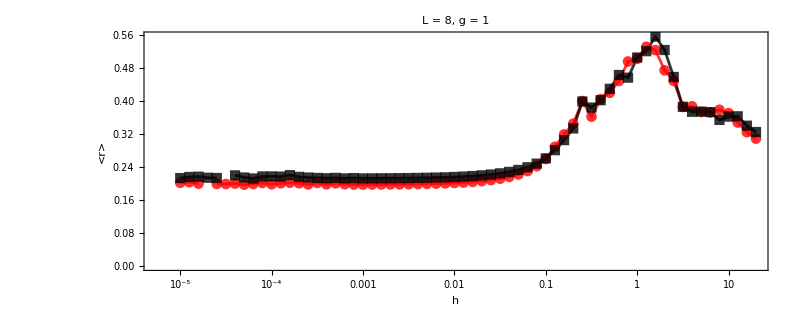

```mathematica
plot=ListLogLinearPlot[{Transpose[{glist,data1[[All,1]][[All,2]]}],Transpose[{glist,data1[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Directive[Red,Opacity[0.8]],Directive[Black,Opacity[0.8]]},PlotTheme->"Detailed",FrameLabel->{Style["h",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", g = 1",25,Black]]
```